```mathematica
Quit[]
```

# L-systems with Turtle Interpretation

## References

Prusinkiewicz P., Lindenmayer A., The Algorithmic Beauty of Plants, Springer-Verlag, NewYork, 1990.

## Definitions

```mathematica
<<Turtle`;
```

### Translate words of L-system into turtle directives

```mathematica
ClearAll[StringToList];
StringToList[string_String]:=Module[
{
rules={
"F"->"Forward",
"f"->"forward",
"+"->"left",
"-"->"right"
},
dirList=StringCases[
string,
RegularExpression["([A-Za-z\\+\\-\\[\\]{}])(\\(([^\\)]+)\\))?"]:>{"$1",StringSplit["$3",","]}
],
outputStack={{}},
top
},
Do[
Switch[dir⟦1⟧,
"[",
	AppendTo[outputStack,{}]; (* Push *),
"]",
	{{top},outputStack}=TakeDrop[outputStack,-1]; (* Pop *)
	AppendTo[outputStack⟦-1⟧,top];,
"F"|"f"|"+"|"-",
	AppendTo[outputStack⟦-1⟧,
	(Replace[dir⟦1⟧,rules])@@ToExpression[dir⟦2⟧]
	];,
_String,
	AppendTo[outputStack⟦-1⟧,dir⟦1⟧@@ToExpression[dir⟦2⟧]];
],
{dir,dirList}
];
Return[First[outputStack]];
]
```

```mathematica
ClearAll[ListToDirectives]
Options[ListToDirectives]={
"Forward"->1,(* distance *)
"forward"->1,(* distance *)
"left"->π/2 ,(* angle *)
"right"->π/2 (* angle *)
};
ListToDirectives[list_List,OptionsPattern[]]:=list/.{
"Forward"[]:>"Forward"[OptionValue["Forward"]],
"forward"[]:>"forward"[OptionValue["forward"]],
"left"[]:>"turn"[OptionValue["left"]],
"right"[]:>"turn"[-OptionValue["right"]],
"left"[ang_]:>"turn"[ang],
"right"[ang_]:>"turn"[-ang]
};
```

## Applications

### 1

#### Example 1.1: Koch island

```mathematica
ω=StringToList["F-F-F-F"];
rules={
"Forward"[]->Sequence@@StringToList["F-F+F+FF-F-F+F"]
};
```

```mathematica
lst=Nest[ReplaceAll[rules],ω,3];
```

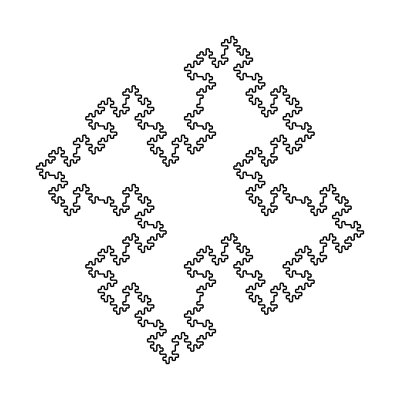

```mathematica
Graphics[ParseDirectives@ListToDirectives[lst]]
```

#### Example 1.2 : Islands and lakes

```mathematica
ω=StringToList["F+F+F+F"];
rules={
"Forward"[]->Sequence@@StringToList["F+f-FF+F+FF+Ff+FF-f+FF-F-FF-Ff-FFF"],
"forward"[]->Sequence@@StringToList["ffffff"]
};
```

```mathematica
lst=Nest[ReplaceAll[rules],ω,2];
```

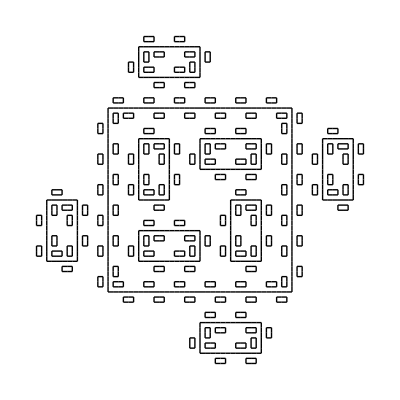

```mathematica
Graphics[ParseDirectives@ListToDirectives[lst]]
```

#### Example 1.3: Sierpiński gasket

```mathematica
ω=StringToList["F(r)"];
rules={
"Forward"[l]->Sequence@@StringToList["F(r)+F(l)+F(r)"],
"Forward"[r]->Sequence@@StringToList["F(l)-F(r)-F(l)"]
};
rulesForNormalization={
"Forward"[l|r]:>"Forward"[]
};
```

```mathematica
lst=Nest[ReplaceAll[rules],ω,6]/.rulesForNormalization;
```

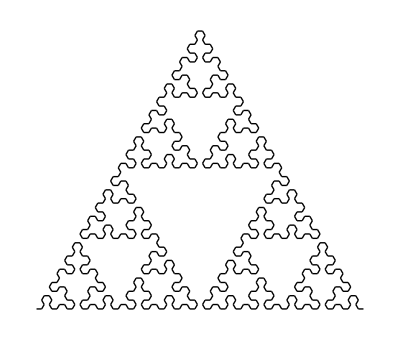

```mathematica
Graphics[ParseDirectives@ListToDirectives[lst,"left"->π/3,"right"->π/3]]
```

### 2

#### Example 2.1: Bracketed OL-system

```mathematica
ω=StringToList["X"];
rules={
"X"[]->Sequence@@StringToList["F-[[X]+X]+F[+FX]-X"],
"Forward"[]->Sequence@@StringToList["FF"]
};
```

```mathematica
lst=Nest[ReplaceAll[rules],ω,5];
```

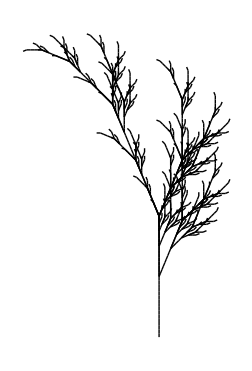

```mathematica
Graphics[
ParseDirectives[
ListToDirectives[lst,"left"->22.5°,"right"->22.5°],
InitialState->{{0,0},90°}
]
]
```

#### Example 2.2 : Binary tree

```mathematica
ω=StringToList["A"];
rules={
"A"[]->Sequence@@StringToList["F(1)[+A][-A]"],
"Forward"[s_]:>Evaluate[Sequence@@StringToList["F(s*R)"]]
};
rulesForConstants={R->1.456};
```

```mathematica
lst=Nest[ReplaceAll[rules],ω,12]/.rulesForConstants;
```

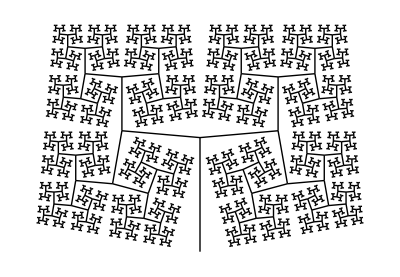

```mathematica
Graphics[
ParseDirectives[
ListToDirectives[lst,"left"->85°,"right"->85°],
InitialState->{{0,0},90°}
]
]
```